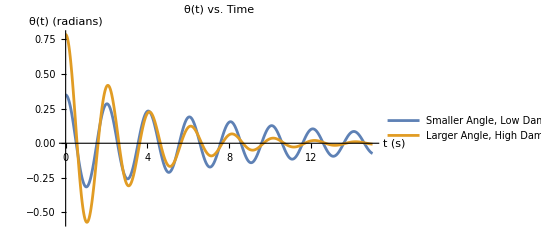

```mathematica
(* General Case *)
g=9.81; (*Acceleration due to gravity in m/s^2*)
L=1; (*Length of the pendulum in meters*)

eqn[beta_]:=θ''[t]+2*beta*θ'[t]+(g/L)*Sin[θ[t]]==0;

θ0Small=π/9; (*20 degrees*)
θ0Large=π/4; (*45 degrees*)
ω0=0; (*Initial angular velocity*)

beta1=0.1; (*Small damping coefficient*)
beta2=0.3; (*Larger damping coefficient*)

solSmall=NDSolve[{eqn[beta1],θ[0]==θ0Small,θ'[0]==ω0},θ,{t,0,15}]; (* Case I: Small angle and small damping *)
solLarge=NDSolve[{eqn[beta2],θ[0]==θ0Large,θ'[0]==ω0},θ,{t,0,15}];  (* Case II: Large angle and small damping *)

Plot[{Evaluate[θ[t]/. solSmall],Evaluate[θ[t]/. solLarge]},{t,0,15},PlotRange->All,PlotLegends->{"Smaller Angle, Low Damping (θ0 = π/9, β = 0.1)","Larger Angle, High Damping (θ0 = π/4, β = 0.3)"},PlotLabel->"θ(t) vs. Time",AxesLabel->{"t (s)","θ(t) (radians)"}]
```

1.00756

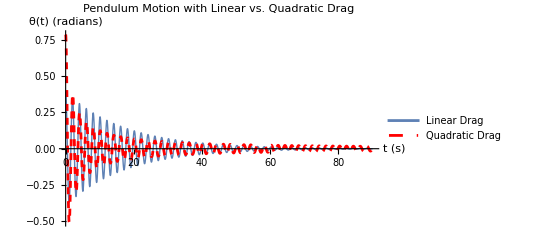

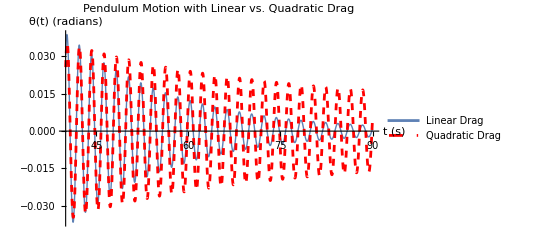

```mathematica
(* Quadratic Damping Case *)
(*Constants*)m=1; (*Mass of the pendulum bob in kg*)
L=1; (*Length of the pendulum in meters*)
g=9.81; (*Acceleration due to gravity in m/s^2*)
rho=1.225; (*Air density in kg/m^3*)
A=1.75; (*Cross-sectional area in m^2*)
CD=0.47; (*Drag coefficient for a sphere*)
b=0.115; (*Linear drag coefficient---you can different value here and try to understand the picture*)
A*CD*rho  (* You can play with this number by changing A as CD and rho are fixed for sphere and air*)

(*Linear drag equation of motion*)
eqnLinear=m*L*θ''[t]+b*L*θ'[t]+m*g*L*Sin[θ[t]]==0;

(*Quadratic drag equation of motion*)
eqnQuadratic=m*L*θ''[t]+(1/2)*CD*rho*A*L^2*Abs[θ'[t]]*θ'[t]+m*g*L*Sin[θ[t]]==0;

(*Initial conditions*)
θ1=π/8; (*Initial angle in radians*)
θ0=π/4; (*Initial angle in radians*)
ω0=0; (*Initial angular velocity*)

(*Solve the differential equations numerically*)
solLinear=NDSolve[{eqnLinear,θ[0]==θ1,θ'[0]==ω0},θ,{t,0,90}];
solQuadratic=NDSolve[{eqnQuadratic,θ[0]==θ0,θ'[0]==ω0},θ,{t,0,90}];

(*Plot the angular displacement over time for both cases*)
Plot[{Evaluate[θ[t]/. solLinear],Evaluate[θ[t]/. solQuadratic]},{t,0,90},PlotRange->All,PlotLegends->{"Linear Drag","Quadratic Drag"},PlotLabel->"Pendulum Motion with Linear vs. Quadratic Drag",AxesLabel->{"t (s)","θ(t) (radians)"},PlotStyle->{{Thick},{Red, Dashed}}]

(*Plot the angular displacement over time for 40 to 70 s*)
Plot[{Evaluate[θ[t]/. solLinear],Evaluate[θ[t]/. solQuadratic]},{t,40,90},PlotRange->All,PlotLegends->{"Linear Drag","Quadratic Drag"},PlotLabel->"Pendulum Motion with Linear vs. Quadratic Drag",AxesLabel->{"t (s)","θ(t) (radians)"},PlotStyle->{{Thick},{Red, Dashed}}]
```